```mathematica
SetDirectory@NotebookDirectory[];
Import["QuESTlink.m"];
CreateLocalQuESTEnv[];
(*Import["https://qtechtheory.org/QuESTlink.m"]
CreateDownloadedQuESTEnv[];*)
```

## Parameters

```mathematica
numQb=4;
numGt=8;
ϵ0=0.02;
ϵ=RandomReal[{0.0,2*ϵ0},2*numGt];
ϵD=0.02;
SamSize=10000;
```

```mathematica
CreateFile["CS-mc"<>"-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-er"<>ToString[ϵ0]<>"-ed"<>ToString[ϵD]<>".dat"];
file=File["CS-mc"<>"-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-er"<>ToString[ϵ0]<>"-ed"<>ToString[ϵD]<>".dat"];
Data={};
AppendTo[Data,"model: coherent rotations and amplitude damping"];
AppendTo[Data,"numQb:"<>ToString[numQb]];
AppendTo[Data,"numGt:"<>ToString[numGt]];
AppendTo[Data,"epsR:"<>ToString[ϵ]];
AppendTo[Data,"epsD:"<>ToString[ϵD]];
AppendTo[Data,"SamSize:"<>ToString[SamSize]];
AppendTo[Data,""];
Export[file,Data];
```

## QC

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
ρIN=CreateDensityQureg[numQb];
ρOUT=CreateDensityQureg[numQb];
ρWP=CreateDensityQureg[numQb];
```

## Gates

```mathematica
PZ={{1.,0.},{0.,-1.}};
PX={{0.,1.},{1.,0.}};
PY={{0.,-ⅈ},{ⅈ,0.}};
iden=IdentityMatrix[2];
Clifford={iden,PX,PY,PZ,(iden+ⅈ PX)/Sqrt[2],(iden-ⅈ PX)/Sqrt[2],(iden+ⅈ PY)/Sqrt[2],(iden-ⅈ PY)/Sqrt[2],(iden+ⅈ PZ)/Sqrt[2],(iden-ⅈ PZ)/Sqrt[2],(PX+PY)/Sqrt[2],(PX-PY)/Sqrt[2],(PX+PZ)/Sqrt[2],(PX-PZ)/Sqrt[2],(PY+PZ)/Sqrt[2],(PY-PZ)/Sqrt[2],(ⅈ iden+PX+PY+PZ)/2,(ⅈ iden-PX-PY+PZ)/2,(ⅈ iden+PX-PY-PZ)/2,(ⅈ iden-PX+PY-PZ)/2,(-ⅈ iden+PX+PY+PZ)/2,(-ⅈ iden-PX-PY+PZ)/2,(-ⅈ iden+PX-PY-PZ)/2,(-ⅈ iden-PX+PY-PZ)/2};
```

```mathematica
uPhase={{1,0,0,ⅈ},{0,1,ⅈ,0},{0,ⅈ,1,0},{ⅈ,0,0,1}}/Sqrt[2];
```

```mathematica
gates=Table[IdentityMatrix[2],numQb+2*numGt];
```

## Circuits

```mathematica
(*experimental circuit*)
GateGraph={3,2,1,0,2,1,0,3,1,0,3,2,2,1,0,3,{0,0,0}};
```

```mathematica
circuitIdeal[numQb_,numGt_,GateGraph_,gates_]:=(
circ={};
Do[(
g=gates[[q+1]];
AppendTo[circ,Subscript[U, q][g]];
),{q,0,numQb-1,1}];
Do[(
q1=GateGraph[[2*t+1]];
q2=GateGraph[[2*t+2]];
AppendTo[circ,Subscript[U, q1,q2][uPhase]];
g=gates[[numQb+2*t+1]];
AppendTo[circ,Subscript[U, q1][g]];
g=gates[[numQb+2*t+2]];
AppendTo[circ,Subscript[U, q2][g]];
),{t,0,numGt-1,1}];
Do[(
If[GateGraph[[2*numGt+1,q]]==1,AppendTo[circ,Subscript[C, q][Subscript[X, 0]]]];
),{q,1,numQb-1,1}];
Return[circ]
)
```

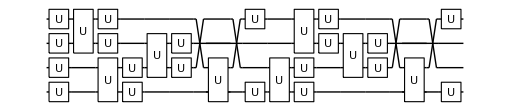

```mathematica
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
DrawCircuit@circI
```

```mathematica
circuitNoisy[numQb_,numGt_,GateGraph_,gates_,ϵ_,ϵD_]:=(
circ={};
Do[(
g=gates[[q+1]];
AppendTo[circ,Subscript[U, q][g]];
),{q,0,numQb-1,1}];
Do[(
q1=GateGraph[[2*t+1]];
q2=GateGraph[[2*t+2]];
AppendTo[circ,Subscript[U, q1,q2][uPhase]];
AppendTo[circ,Subscript[Rx, q1][2*N[π,12]*ϵ[[2*t+1]]]];AppendTo[circ,Subscript[Rx, q2][2*N[π,12]*ϵ[[2*t+1]]]];AppendTo[circ,Subscript[Rz, q1][2*N[π,12]*ϵ[[2*t+2]]]];AppendTo[circ,Subscript[Rz, q2][2*N[π,12]*ϵ[[2*t+2]]]];
AppendTo[circ,Subscript[Damp, q1][ϵD]];AppendTo[circ,Subscript[Damp, q2][ϵD]];
g=gates[[numQb+2*t+1]];
AppendTo[circ,Subscript[U, q1][g]];
g=gates[[numQb+2*t+2]];
AppendTo[circ,Subscript[U, q2][g]];
),{t,0,numGt-1,1}];
Do[(
If[GateGraph[[2*numGt+1,q]]==1,AppendTo[circ,Subscript[C, q][Subscript[X, 0]]]];
),{q,1,numQb-1,1}];
Return[circ]
)
```

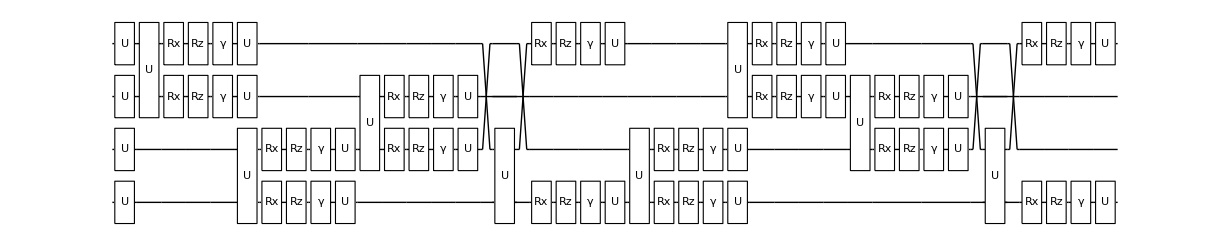

```mathematica
circN=circuitNoisy[numQb,numGt,GateGraph,gates,ϵ,ϵD];
DrawCircuit@circN
```

## Sampling

```mathematica
SamplingU[numQb_,numGt_,GateGraph_,ϵ_,ϵD_,SamSize_]:=(
Err={};
Fid={};
Do[(
gates=RandomVariate[CircularUnitaryMatrixDistribution[2],numQb+2*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
circN=circuitNoisy[numQb,numGt,GateGraph,gates,ϵ,ϵD];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circN,ρIN,ρOUT];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[Err,(ZN-ZI)/2];
AppendTo[Fid,1-CalcFidelity[ρOUT,ψOUT]];
),SamSize];
Return[{Err,Fid}]
)
```

```mathematica
SamplingC[numQb_,numGt_,GateGraph_,ϵ_,ϵD_,SamSize_]:=(
Err={};
Fid={};
Do[(
gates=RandomChoice[Clifford,numQb+2*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,gates];
circN=circuitNoisy[numQb,numGt,GateGraph,gates,ϵ,ϵD];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circN,ρIN,ρOUT];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[Err,(ZN-ZI)/2];
AppendTo[Fid,1-CalcFidelity[ρOUT,ψOUT]];
),SamSize];
Return[{Err,Fid}]
)
```

## Simulation

```mathematica
StartTime = Now
US=SamplingU[numQb,numGt,GateGraph,ϵ,ϵD,SamSize];
CS=SamplingC[numQb,numGt,GateGraph,ϵ,ϵD,SamSize];
EndTime = Now
```

Tue 14 Jul 2020 16:47:55GMT-4.

Tue 14 Jul 2020 16:49:52GMT-4.

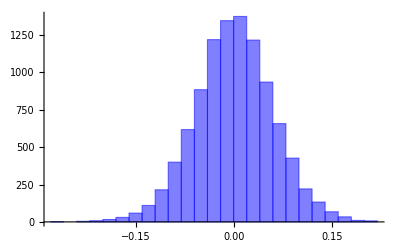

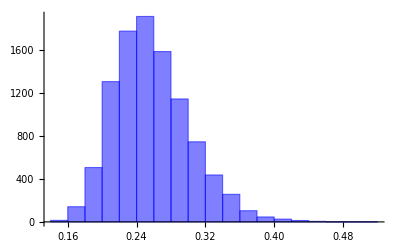

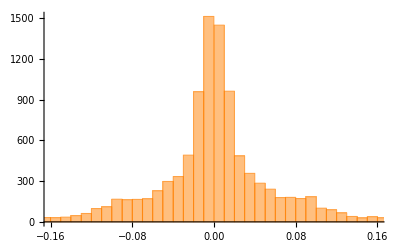

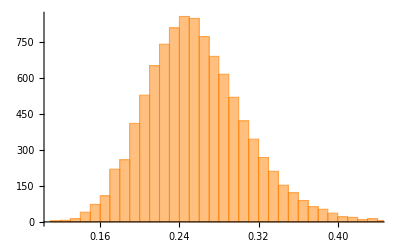

```mathematica
Histogram[US[[1]],ChartStyle->Opacity[.5,Blue]]
Histogram[US[[2]],ChartStyle->Opacity[.5,Blue]]
Histogram[CS[[1]],ChartStyle->Opacity[.5,Orange]]
Histogram[CS[[2]],ChartStyle->Opacity[.5,Orange]]

AppendTo[Data,"US-Err:"];AppendTo[Data,US[[1]]];AppendTo[Data,""];
AppendTo[Data,"US-Fid:"];AppendTo[Data,US[[2]]];AppendTo[Data,""];
AppendTo[Data,"CS-Err:"];AppendTo[Data,CS[[1]]];AppendTo[Data,""];
AppendTo[Data,"CS-Fid:"];AppendTo[Data,CS[[2]]];AppendTo[Data,""];
AppendTo[Data,"Start Time: "<>ToString[StartTime]];
AppendTo[Data,"End Time: "<>ToString[EndTime]];
Export[file,Data];
```

```mathematica
MUS=Table[Moment[US[[1]],m],{m,1,10,1}]
MCS=Table[Moment[CS[[1]],m],{m,1,10,1}]
MUS=Table[Moment[US[[2]],m],{m,1,10,1}]
MCS=Table[Moment[CS[[2]],m],{m,1,10,1}]
```

{0.00110559,0.00356687,1.03952×10^-6,0.0000426017,-4.93536×10^-7,9.15845×10^-7,-3.649×10^-8,2.86519×10^-8,-2.32888×10^-9,1.16001×10^-9}

{0.000476473,0.00349244,8.03859×10^-6,0.0000695354,3.49096×10^-7,2.5719×10^-6,1.83793×10^-8,1.32613×10^-7,7.57757×10^-10,8.3119×10^-9}

{0.258023,0.0684795,0.0187057,0.00526197,0.00152515,0.000455698,0.000140422,0.0000446424,0.000014647,4.96048×10^-6}

{0.257424,0.068809,0.0190917,0.00549828,0.00164388,0.000510425,0.000164671,0.0000552243,0.0000192583,6.98405×10^-6}